```mathematica
sol=DSolve[{x'[t]==y[t], y'[t]==x[t],x[0]==2,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→ⅇ^-t (1+ⅇ^(2 t)),y[t]→ⅇ^-t (-1+ⅇ^(2 t))}}

```mathematica
fun = Table[sol[[1]][[i]][[2]],{i,1,Length[sol[[1]]]}];
```

```mathematica
euler=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\ImplicitEuler.txt",Number,RecordLists->True];
adams=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\AdamsBashford.txt",Number,RecordLists->True];
```

```mathematica
PredictionCorection=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\PredictionCorection.txt",Number,RecordLists->True];
```

```mathematica
tau = 0.1;T=1;
```

```mathematica
timetable = Table[i,{i,0,T,tau}];
```

```mathematica
n = Length[euler[[1]]];
```

```mathematica
dotseuler = Table[euler[[All,i]],{i,1,n}];
```

{{2,2.0202,2.06101,2.12306,2.20717,2.31443,2.44615,2.60391,2.78956,3.00527,3.25352,3.53713,3.85934,4.22378,4.63457,5.09633,5.61422,6.19406,6.84232,7.56624,8.37391,9.27431,10.2775,11.3946,12.6381,14.0219,15.5612,17.2733,19.1771,21.2939,23.6471,26.263,29.1706,32.4022,35.9938,39.9852,44.4208,49.3499,54.8273,60.9138,67.6771,75.1923,83.5429,92.8218,103.132,114.588,127.317,141.461,157.177,174.639,194.041,215.599,239.553,266.169,295.742,328.601,365.111,405.678,450.753,500.835,556.483,618.314,687.015,763.349,848.165,942.406,1047.12,1163.46,1292.74,1436.37,1595.97,1773.3,1970.33,2189.26,2432.51,2702.79,3003.1,3336.77,3707.53,4119.47,4577.19,5085.77,5650.86,6278.73,6976.37,7751.52,8612.8,9569.77,10633.1,11814.5,13127.3,14585.8,16206.5,18007.2,20008,22231.1,24701.3,27445.8,30495.4,33883.8,37648.6},{0,0.20202,0.408122,0.620427,0.841144,1.07259,1.3172,1.57759,1.85655,2.15708,2.48243,2.83614,3.22208,3.64445,4.10791,4.61754,5.17897,5.79837,6.4826,7.23923,8.07662,9.00405,10.0318,11.1713,12.4351,13.8373,15.3934,17.1207,19.0384,21.1678,23.5325,26.1588,29.0759,32.3161,35.9155,39.914,44.3561,49.2911,54.7738,60.8652,67.6329,75.1521,83.5064,92.7886,103.102,114.561,127.292,141.438,157.156,174.62,194.024,215.584,239.539,266.156,295.73,328.59,365.102,405.669,450.745,500.828,556.477,618.308,687.009,763.344,848.161,942.401,1047.11,1163.46,1292.73,1436.37,1595.97,1773.3,1970.33,2189.26,2432.51,2702.79,3003.1,3336.77,3707.53,4119.47,4577.19,5085.77,5650.86,6278.73,6976.36,7751.52,8612.8,9569.77,10633.1,11814.5,13127.3,14585.8,16206.5,18007.2,20008,22231.1,24701.3,27445.8,30495.4,33883.8,37648.6}}

```mathematica
dotsadams=Table[adams[[All,i]],{i,1,n}];
```

{{2,2,2.02,2.06,2.13046,2.22245,2.33675,2.47415,2.63653,2.8252,3.04217,3.28957,3.56991,3.88597,4.24092,4.63831,5.08212,5.57679,6.12727,6.73907,7.41831,8.17179,9.00706,9.93246,10.9573,12.0917,13.3472,14.7363,16.2728,17.9722,19.8514,21.9293,24.2267,26.7665,29.5742,32.6779,36.1086,39.9006,44.092,48.7247,53.8449,59.5041,65.7587,72.6714,80.3114,88.7552,98.0872,108.401,119.799,132.397,146.319,161.706,178.711,197.504,218.274,241.229,266.597,294.634,325.619,359.863,397.709,439.534,485.759,536.844,593.303,655.699,724.657,800.867,885.092,978.174,1081.05,1194.74,1320.38,1459.25,1612.71,1782.32,1969.76,2176.91,2405.85,2658.87,2938.5,3247.53,3589.07,3966.52,4383.67,4844.69,5354.2,5917.29,6539.59,7227.35,7987.43,8827.45,9755.81,10781.8,11915.7,13168.8,14553.8,16084.4,17775.9,19645.4,21711.4},{0,0.2,0.4,0.602,0.810833,1.02906,1.25647,1.49682,1.7521,2.02498,2.31808,2.6344,2.97707,3.34955,3.75554,4.19912,4.68472,5.2172,5.8019,6.44466,7.15192,7.93076,8.78896,9.73512,10.7787,11.9302,13.201,14.604,16.1531,17.8639,19.7534,21.8406,24.1465,26.6939,29.5085,32.6184,36.0548,39.852,44.048,48.6848,53.8089,59.4715,65.7292,72.6447,80.2873,88.7333,98.0674,108.383,119.783,132.382,146.306,161.694,178.7,197.494,218.265,241.221,266.59,294.627,325.613,359.858,397.704,439.53,485.755,536.841,593.299,655.696,724.654,800.864,885.089,978.172,1081.04,1194.74,1320.38,1459.25,1612.71,1782.32,1969.76,2176.91,2405.85,2658.87,2938.5,3247.53,3589.07,3966.52,4383.67,4844.69,5354.2,5917.29,6539.59,7227.35,7987.43,8827.45,9755.81,10781.8,11915.7,13168.8,14553.8,16084.4,17775.9,19645.4,21711.4}}

```mathematica
dotsPredictionCorection=Table[PredictionCorection[[All,i]],{i,1,n}];
```

{{2,2,2.02,2.06,2.13056,2.22252,2.33667,2.47423,2.63654,2.82525,3.04223,3.28966,3.57001,3.88609,4.24107,4.63849,5.08234,5.57705,6.12758,6.73943,7.41874,8.17229,9.00764,9.93314,10.9581,12.0926,13.3483,14.7375,16.2742,17.9737,19.8532,21.9314,24.2291,26.7692,29.5773,32.6814,36.1126,39.9052,44.0972,48.7305,53.8516,59.5116,65.7672,72.681,80.3223,88.7675,98.1011,108.416,119.817,132.417,146.342,161.731,178.739,197.536,218.311,241.27,266.643,294.686,325.678,359.929,397.782,439.617,485.852,536.949,593.42,655.83,724.804,801.032,885.278,978.383,1081.28,1195,1320.68,1459.58,1613.08,1782.73,1970.22,2177.43,2406.43,2659.52,2939.23,3248.35,3589.98,3967.54,4384.81,4845.97,5355.62,5918.88,6541.37,7229.34,7989.66,8829.94,9758.59,10784.9,11919.2,13172.7,14558.1,16089.2,17781.3,19651.4,21718.2},{0,0.2,0.4,0.602,0.811226,1.02874,1.25651,1.49686,1.75219,2.02505,2.31818,2.63451,2.97721,3.3497,3.75572,4.19933,4.68497,5.2175,5.80224,6.44506,7.15238,7.93128,8.78956,9.73581,10.7795,11.9311,13.2021,14.6052,16.1545,17.8655,19.7552,21.8427,24.1488,26.6966,29.5116,32.6219,36.0588,39.8565,44.0531,48.6907,53.8155,59.479,65.7377,72.6543,80.2981,88.7456,98.0813,108.399,119.801,132.402,146.328,161.719,178.728,197.527,218.302,241.262,266.636,294.679,325.672,359.923,397.778,439.613,485.848,536.945,593.417,655.827,724.802,801.03,885.275,978.381,1081.28,1195,1320.68,1459.57,1613.08,1782.73,1970.22,2177.43,2406.43,2659.52,2939.23,3248.35,3589.98,3967.54,4384.81,4845.97,5355.62,5918.88,6541.37,7229.34,7989.65,8829.94,9758.59,10784.9,11919.2,13172.7,14558.1,16089.2,17781.3,19651.4,21718.2}}

```mathematica
pointseuler  = Table[Table[{timetable[[j]],dotseuler [[i]][[j]]},{j,1,Length[timetable]}],{i,1,n}];
```

```mathematica
pointsadams  = Table[Table[{timetable[[j]],dotsadams [[i]][[j]]},{j,1,Length[timetable]}],{i,1,n}];
```

```mathematica
pointsPredictionCorection  = Table[Table[{timetable[[j]],dotsPredictionCorection [[i]][[j]]},{j,1,Length[timetable]}],{i,1,n}];
```

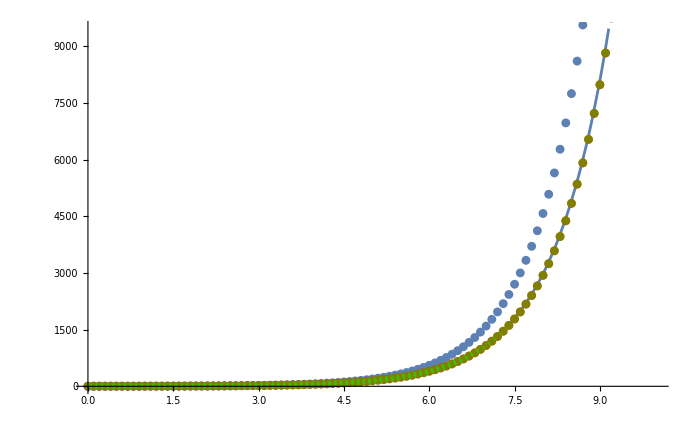
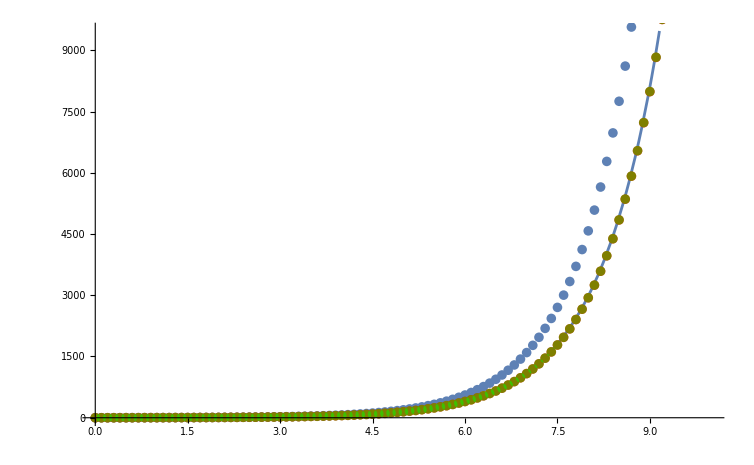

```mathematica
Paints = Table[Show[Plot[fun[[i]],{t,0,T}], ListPlot[pointseuler[[i]]], ListPlot[pointsadams[[i]], PlotStyle->Red], ListPlot[pointsPredictionCorection[[i]], PlotStyle->{Green, Opacity[0.5]}]],{i,1,n}]
```